```mathematica
(* Base Tabu Inertia *)
inertiaData20 = {{5, 703.16}, {10,703.16}, {30, 703.16}};
inertiaData50 = {{5, 1103.10}, {10,1438.80}, {30, 1601.32}};
inertiaData100 = {{5, 1561.84}, {10, 1109.09}, {30,1494.35}};
```

```mathematica
iplot20= ListLinePlot[inertiaData20,
PlotStyle-> {Red}];
iplot50= ListLinePlot[inertiaData50,
PlotStyle-> {Green}];
iplot100= ListLinePlot[inertiaData100,
PlotStyle-> {Blue}];
```

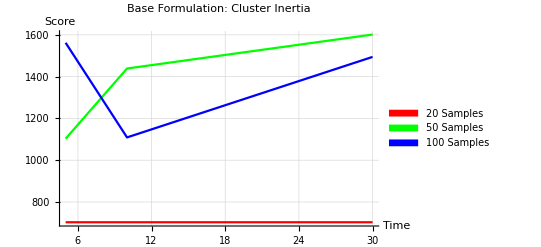

```mathematica
Legended[
Show[iplot20,iplot50, iplot100,
PlotLabel-> "Base Formulation: Cluster Inertia",
AxesLabel-> {"Time", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Green, Blue}, {"20 Samples", "50 Samples", "100 Samples"}]
]
```

```mathematica
(* Base Tabu Silhouette Scores*)
```

```mathematica
sscoreData20 = { {5,0.35}, {10, 0.35}, {30, 0.35}};
sscoreData50 = { {5, 0.19}, {10, 0.24}, {30, 0.32}};
sscoreData100 = { {5, 0.04}, {10, 0.015}, {30, 0.40}};

splot20= ListLinePlot[sscoreData20,
PlotStyle-> {Red}];
splot50= ListLinePlot[sscoreData50,
PlotStyle-> {Green}];
splot100= ListLinePlot[sscoreData100,
PlotStyle-> {Blue}];
```

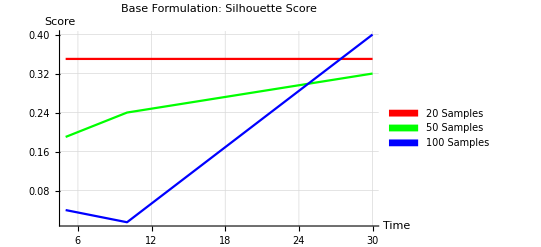

ListPlot::lpn: TagBox[RowBox[{\"(\", \"\", GridBox[{{\"5.\", \"703.16\"},{\"10.\", \"703.16\"},{\"30.\", \"703.16\"}
   },GridBoxAlignment->{\"Columns\" -> {{Center}}, \"Rows\" -> {{Baseline}}},GridBoxSpacings->{\"Columns\" -> {Offset[0.28], {Offset[0.7]}, Offset[0.28]}, \"Rows\" -> {Offset[0.2], {Offset[0.4]}, Offset[0.2]}}], \"\", \")\"}],Function[BoxForm`e$, MatrixForm[BoxForm`e$]]] is not a list of numbers or pairs of numbers.

```mathematica
Legended[
Show[splot20,splot50, splot100,
PlotLabel-> "Base Formulation: Silhouette Score",
AxesLabel-> {"Time", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Green, Blue}, {"20 Samples", "50 Samples", "100 Samples"}]
]
```

```mathematica
(* Base Tabu Homogeneity Scores *)
```

```mathematica
hscoreData20 = {{5, 0.36}, {10, 0.36}, {30, 0.36}};
hscoreData50 = {{5, 0.16}, {10, 0.22}, {30, 0.33}};
hscoreData100 = {{5,0.01}, {10,0.05}, {30, 0.009}};

hplot20= ListLinePlot[hscoreData20,
PlotStyle-> {Red}];
hplot50= ListLinePlot[hscoreData50,
PlotStyle-> {Green}];
hplot100= ListLinePlot[hscoreData100,
PlotStyle-> {Blue}];
```

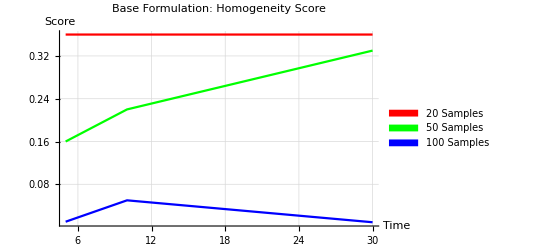

```mathematica
Legended[
Show[hplot20,hplot50, hplot100,
PlotLabel-> "Base Formulation: Homogeneity Score",
AxesLabel-> {"Time", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Green, Blue}, {"20 Samples", "50 Samples", "100 Samples"}]
]
```

```mathematica
(* Base Tabu Completness Score *)

cscoreData20={{5,0.38},{10,0.38},{30,0.38}};
cscoreData50={{5,0.18},{10,0.26},{30,0.33}};
cscoreData100={{5,0.19},{10,0.07},{30,0.19}};
```

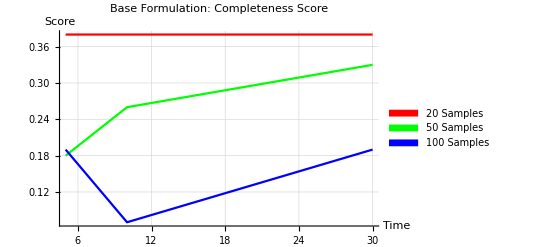

```mathematica
cplot20= ListLinePlot[cscoreData20,
PlotStyle-> {Red}];
cplot50= ListLinePlot[cscoreData50,
PlotStyle-> {Green}];
cplot100= ListLinePlot[cscoreData100,
PlotStyle-> {Blue}];


Legended[
Show[cplot20,cplot50, cplot100,
PlotLabel-> "Base Formulation: Completeness Score",
AxesLabel-> {"Time", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Green, Blue}, {"20 Samples", "50 Samples", "100 Samples"}]
]
```

```mathematica
(* Base Tabu V-Measure *)
```

```mathematica
vscoreData20 = { {5,0.37}, {10,0.37},{30, 0.37}};
vscoreData50 = { {5,0.17}, {10,0.24}, {30,0.33}};
vscoreData100 = { {5,0.01},{10,0.06}, {30,0.018}};
```

```mathematica
vplot20= ListLinePlot[cscoreData20,
PlotStyle-> {Red}];
vplot50= ListLinePlot[cscoreData50,
PlotStyle-> {Green}];
vplot100= ListLinePlot[cscoreData100,
PlotStyle-> {Blue}];
```

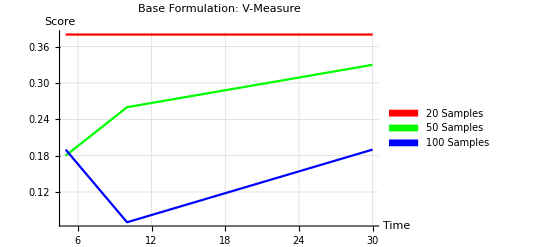

```mathematica
Legended[
Show[vplot20,vplot50, vplot100,
PlotLabel-> "Base Formulation: V-Measure",
AxesLabel-> {"Time", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Green, Blue}, {"20 Samples", "50 Samples", "100 Samples"}]
]
```

```mathematica
(* Simulated Annealing *)
```

```mathematica
simInertia={ {20,546.67},{30,1465.74},{35,3057.51},{40,3921.44},{45,5525.67}};
simSil={ {20, 0.13},{30, -0.15},{35,-0.06},{40,-0.02},{45,-0.10}};
simHomog={ {20,0.20},{30,0.10},{35,0.03},{40,0.27},{45,0.03}};
simComp={{20,0.20},{30,0.10},{35,0.03},{40,0.28},{45,0.04}};
simV={{20,0.20},{30,0.10},{35,0.03},{40,0.27},{45,0.03}};
```

```mathematica
(* Sim Anneal Inertia *)
```

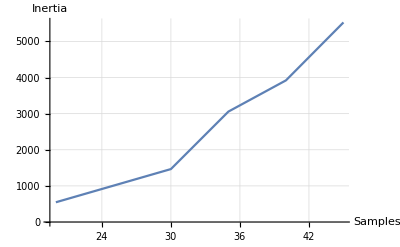

```mathematica
ListLinePlot[simInertia,
(* PlotLabel-> "Base Formulation: Simulated Annealing Cluster Inertia", *)
AxesLabel->{"Samples", "Inertia"},
GridLines->Automatic,
PlotRange->Automatic]
```

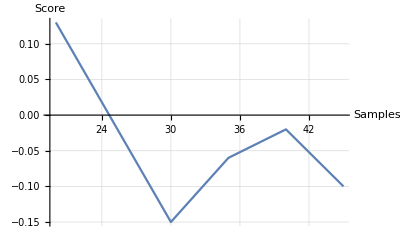

```mathematica
(* Sim Anneal Silhouette *)

ListLinePlot[simSil,
(* PlotLabel-> "Base Formulation: Simulated Annealing Silhouette Score", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]
```

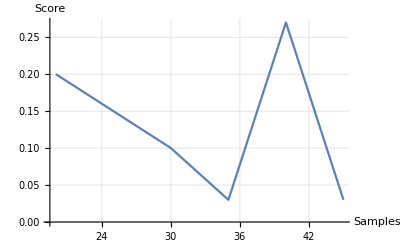

```mathematica
(* Sim Anneal Homogeneity *)

ListLinePlot[simHomog,
(* PlotLabel-> "Base Formulation: Simulated Annealing Homogeneity", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]
```

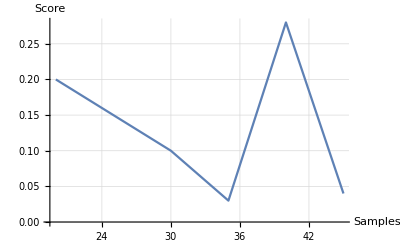

```mathematica
(* Sim Anneal Completenes *)

ListLinePlot[simComp,
(* PlotLabel-> "Base Formulation: Simulated Annealing Completeness Score", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]
```

```mathematica
(* Sim Anneal V-Measure *)

ListLinePlot[simV,
(* PlotLabel-> "Base Formulation: Simulated Annealing V-Measure", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]
```

```mathematica
(* All on One Sim Annealing *)
```

```mathematica
simInertiaPlot= ListLinePlot[simInertia,
PlotStyle-> {Red}];
simSilPlot= ListLinePlot[simSil,
PlotStyle-> {Red}];
simHomogPlot= ListLinePlot[simHomog,
PlotStyle-> {Yellow}];
```

```mathematica
simCompPlot= ListLinePlot[simComp,
PlotStyle-> {Black}];
```

```mathematica
simVPlot= ListLinePlot[simV,
PlotStyle-> {Orange}];
```

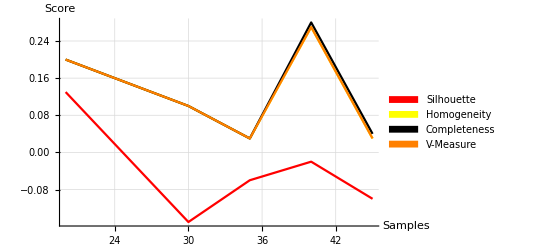

```mathematica
Legended[
Show[simSilPlot, simHomogPlot,simCompPlot, simVPlot,
(* PlotLabel-> "Base Formulation: V-Measure", *)
AxesLabel-> {"Samples", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Yellow, Black, Orange}, {"Silhouette", "Homogeneity", "Completeness", "V-Measure"}]
]
```

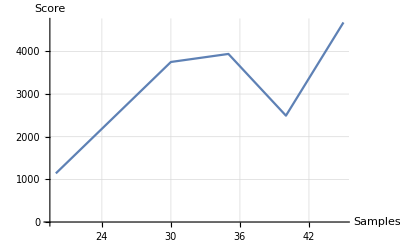

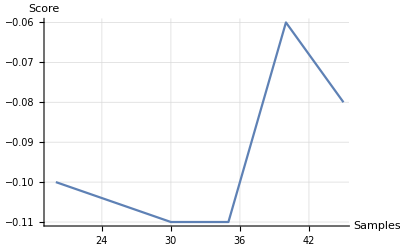

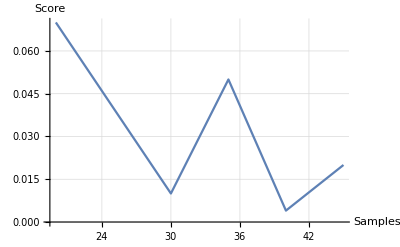

-Graphics-

-Graphics-

```mathematica
(*** Hybrid BQM ***)

hybridInertia={{20,1140.36},{30,3752.20},{35,3940.53},{40,2493.88},{45,4679.08}};
hybridSil={{20,-0.10},{30,-0.11},{35,-0.11},{40,-0.06},{45,-0.08}};
hybridHomog={{20,0.07},{30,0.01},{35,0.05},{40,0.004},{45,0.02}};
hybridComp={{20,0.07},{30,0.01},{35,0.05},{40,0.004},{45,0.02}};
hybridV={{20,0.07},{30,0.01},{35,0.05},{40,0.004},{45,0.02}};


(* Hybrid BQM Inertia *)
ListLinePlot[hybridInertia,
(* PlotLabel-> "Base Formulation: Hybrid BQM Inertia ", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]



(* Hybrid BQM Silhouette *)
ListLinePlot[hybridSil,
(* PlotLabel-> "Base Formulation: Hybrid BQM Silhouette", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]

(* Hybrid BQM Homogeneity *)
ListLinePlot[hybridHomog,
(* PlotLabel-> "Base Formulation: Hybrid BQM Homogeneity ", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]

(* Hybrid BQM Completeness *)
ListLinePlot[hybridComp,
(* PlotLabel-> "Base Formulation: Hybrid BQM Completeness", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]

(* Hybrid BQM V-measure *)
ListLinePlot[hybridV,
(* PlotLabel-> "Base Formulation: Hybrid BQM V-Measure", *)
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic]
```

```mathematica
(* Kmeans Default*)
```

```mathematica
(* kmDefIner  = { {20,33.94 }, {30, 43.30}, {35, 49.05}, {40, 56.83}, {45,63.74 }, {50, 70.59}, {100, 167.75} };

kmDefSil = { {20, 0.54}, {30, 0.56}, {35, 0.54}, {40, 0.52}, {45, 0.52}, {50, 0.53}, {100, 0.44} };

kmDefHomog = { {20, 0.73},{ 30, 0.56}, {35, 0.82}, {40, 0.70}, {45, 0.72}, {50, 0.65}, {100, 0.69} };

kmDefComp= { {20,0.74 }, {30, 0.69}, {35, 0.82}, {40, 0.70}, {45, 0.73}, {50, 0.65}, {100, 0.69} };

kmDefVm = { {20, 0.74}, {30, 0.70}, {35, 0.82}, {40, 0.70}, {45, 0.72}, {50, 0.65}, {100, 0.69} };

kmDefIter = { {20, 2}, {30, 4}, {35, 5}, {40, 3}, {45, 2}, {50, 4}, {100, 5}}; *)


kmDefIner  = { {20,33.94 }, {30, 43.30}, {35, 49.05}, {40, 56.83}, {45,63.74 } };
kmDefSil = { {20, 0.54}, {30, 0.56}, {35, 0.54}, {40, 0.52}, {45, 0.52} };
kmDefHomog = { {20, 0.73},{ 30, 0.56}, {35, 0.82}, {40, 0.70}, {45, 0.72} };
kmDefComp= { {20,0.74 }, {30, 0.69}, {35, 0.82}, {40, 0.70}, {45, 0.73} };
kmDefVm = { {20, 0.74}, {30, 0.70}, {35, 0.82}, {40, 0.70}, {45, 0.72} };
kmDefIter = { {20, 2}, {30, 4}, {35, 5}, {40, 3}, {45, 2}};
```

```mathematica
(* kmTabuIner = {{20,83.83},{30,43.30},{35,49.80},{40,56.83},{45,131.04},{50,70.75},{100,167.75}};
kmTabuSil = {{20,0.31},{30,0.56},{35,0.53},{40,0.52},{45,0.30},{50,0.53},{100,0.44}};
kmTabuHomog = {{20,0.46},{30,0.69},{35,0.76},{40,0.70},{45,0.43},{50,0.68},{100,0.69}};
kmTabuComp= {{20,0.64},{30,0.70},{35,0.76},{40,0.70},{45,0.59},{50,0.68},{100,0.69}};
kmTabuVm = {{20,0.54},{30,0.70},{35,0.76},{40,0.70},{45,0.50},{50,0.68},{100,0.69}};
kmTabuIter = { {20, 4}, {30, 4}, {35, 5}, {40,5}, {45, 4}, {50, 7}, {100, 9}}; *)

kmTabuIner = {{20,83.83},{30,43.30},{35,49.80},{40,56.83},{45,131.04}};
kmTabuSil = {{20,0.31},{30,0.56},{35,0.53},{40,0.52},{45,0.30}};
kmTabuHomog = {{20,0.46},{30,0.69},{35,0.76},{40,0.70},{45,0.43}};
kmTabuComp= {{20,0.64},{30,0.70},{35,0.76},{40,0.70},{45,0.59}};
kmTabuVm = {{20,0.54},{30,0.70},{35,0.76},{40,0.70},{45,0.50}};
kmTabuIter = { {20, 4}, {30, 4}, {35, 5}, {40,5}, {45, 4}};

kmSimAIner={{20,33.94},{30,43.30},{35,114.75},{40, 57.02},{45,64.90}};
kmSimASil={{20,0.54},{30,0.56},{35,0.27},{40,0.52},{45,0.51}};
kmSimAHomog={{20,0.73},{30,0.69},{35,0.41},{40,0.70},{45,0.62}};
kmSimAComp={{20,0.74},{30,0.70},{35,0.54},{40,0.70},{45,0.63}};
kmSimAVm={{20,0.74},{30,0.70},{35,0.47},{40,0.70},{45,0.63}};
kmSimAIter = { {20, 7}, {30, 8}, {35, 5}, {40, 5}, {45, 9}};

kmHybridIner={{20,77.68},{30,43.30},{35,113.91},{40,57.66},{45,64.90},{50,},{100,}};
kmHybridSil={{20,0.24},{30,0.56},{35,0.22},{40,0.52},{45,0.51}};
kmHybridHomog={{20,0.42},{30,0.69},{35,0.52},{40,0.63},{45,0.62}};
kmHybridComp={{20,0.58},{30,0.70},{35,0.63},{40,0.63},{45,0.63}};
kmHybridVm={{20,0.49},{30,0.70},{35,0.57},{40,0.63},{45,0.63}};
kmHybridIter = { {20, 4}, {30, 6}, {35, 5}, {40, 5}, {45, 9} };
```

```mathematica
(* 6 plots, inertia, silhouette, homogeneity, completnetess, v-measure, iterations *)

(* Default Kmeans *)
kmDefInerPlot= ListLinePlot[kmDefIner, PlotStyle-> {Red}];
kmDefSilPlot= ListLinePlot[kmDefSil, PlotStyle-> {Red}];
kmDefHomogPlot= ListLinePlot[kmDefHomog, PlotStyle-> {Red}];
kmDefCompPlot= ListLinePlot[kmDefComp, PlotStyle-> {Red}];
kmDefVmPlot= ListLinePlot[kmDefVm, PlotStyle-> {Red}];
kmDefIterPlot= ListLinePlot[kmDefIter, PlotStyle-> {Red}];

(* Tabu Kmeans *)

kmTabuInerPlot=ListLinePlot[kmTabuIner, PlotStyle-> {Green}];
kmTabuSilPlot=ListLinePlot[kmTabuSil, PlotStyle-> {Green}];
kmTabuHomogPlot=ListLinePlot[kmTabuHomog, PlotStyle-> {Green}];
kmTabuCompPlot=ListLinePlot[kmTabuComp, PlotStyle-> {Green}];
kmTabuVmPlot=ListLinePlot[kmTabuVm, PlotStyle-> {Green}];
kmTabuIterPlot=ListLinePlot[kmTabuIter, PlotStyle-> {Green}];

(* Sim Anneal Kmeans *)

kmSimAInerPlot=ListLinePlot[kmSimAIner, PlotStyle-> {Blue}];
kmSimASilPlot=ListLinePlot[kmSimASil, PlotStyle-> {Blue}];
kmSimAHomogPlot=ListLinePlot[kmSimAHomog, PlotStyle-> {Blue}];
kmSimACompPlot=ListLinePlot[kmSimAComp, PlotStyle-> {Blue}];
kmSimAVmPlot=ListLinePlot[kmSimAVm, PlotStyle-> {Blue}];
kmSimAIterPlot=ListLinePlot[kmSimAIter, PlotStyle-> {Blue}];


(* Hybrid BQM Kmeans *)
```

ListLinePlot::lpn: kmDefIner is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmDefSil is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmDefHomog is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmDefComp is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmDefVm is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmDefIter is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmTabuIner is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmTabuSil is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmTabuHomog is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmTabuComp is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmTabuVm is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmTabuIter is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmSimAIner is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmSimASil is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmSimAHomog is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmSimAComp is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmSimAVm is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: kmSimAIter is not a list of numbers or pairs of numbers.

```mathematica
kmHybridInerPlot=ListLinePlot[kmHybridIner, PlotStyle-> {Black}];
kmHybridSilPlot=ListLinePlot[kmHybridSil, PlotStyle-> {Black}];
kmHybridHomogPlot=ListLinePlot[kmHybridHomog, PlotStyle-> {Black}];
kmHybridCompPlot=ListLinePlot[kmHybridComp, PlotStyle-> {Black}];
kmHybridVmPlot=ListLinePlot[kmHybridVm, PlotStyle-> {Black}];
kmHybridIterPlot=ListLinePlot[kmHybridIter, PlotStyle-> {Black}];
```

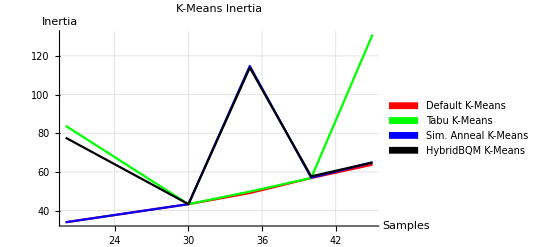

```mathematica
Legended[
Show[kmDefInerPlot,kmTabuInerPlot, kmSimAInerPlot, kmHybridInerPlot,
PlotLabel-> "K-Means Inertia",
AxesLabel-> {"Samples", "Inertia"},
PlotRange->All,
GridLines->Automatic],
(* PlotStyle-> {Red, Green, Blue, Yellow}, *)
SwatchLegend[{Red, Green, Blue, Black}, {"Default K-Means", "Tabu K-Means", "Sim. Anneal K-Means", "HybridBQM K-Means"}]
]
```

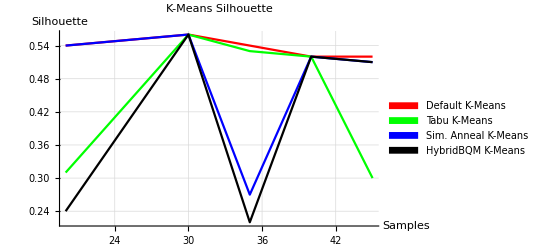

```mathematica
Legended[Show[kmDefSilPlot,kmTabuSilPlot,kmSimASilPlot,kmHybridSilPlot,PlotLabel->"K-Means Silhouette",AxesLabel->{"Samples","Silhouette"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default K-Means","Tabu K-Means","Sim. Anneal K-Means","HybridBQM K-Means"}]]
```

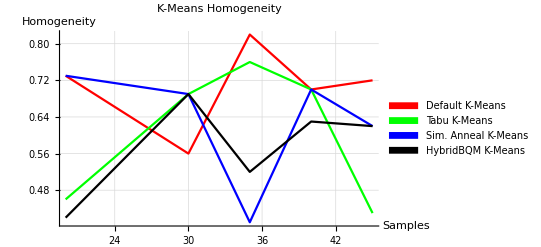

```mathematica
Legended[Show[kmDefHomogPlot,kmTabuHomogPlot,kmSimAHomogPlot,kmHybridHomogPlot,PlotLabel->"K-Means Homogeneity",AxesLabel->{"Samples","Homogeneity"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default K-Means","Tabu K-Means","Sim. Anneal K-Means","HybridBQM K-Means"}]]
```

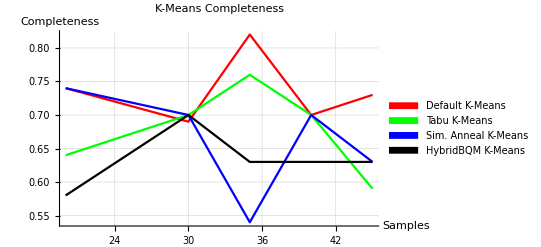

```mathematica
Legended[Show[kmDefCompPlot,kmTabuCompPlot,kmSimACompPlot,kmHybridCompPlot,PlotLabel->"K-Means Completeness",AxesLabel->{"Samples","Completeness"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default K-Means","Tabu K-Means","Sim. Anneal K-Means","HybridBQM K-Means"}]]
```

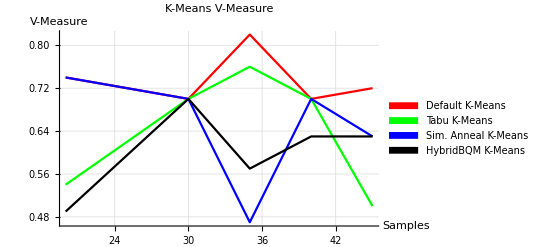

```mathematica
Legended[Show[kmDefVmPlot,kmTabuVmPlot,kmSimAVmPlot,kmHybridVmPlot,PlotLabel->"K-Means V-Measure",AxesLabel->{"Samples","V-Measure"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default K-Means","Tabu K-Means","Sim. Anneal K-Means","HybridBQM K-Means"}]]
```

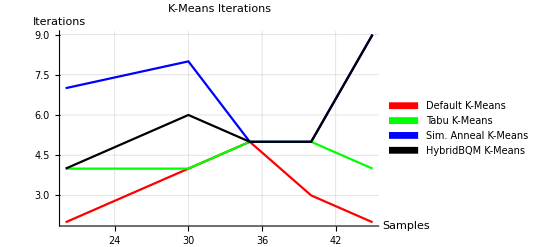

```mathematica
Legended[Show[kmDefIterPlot,kmTabuIterPlot,kmSimAIterPlot,kmHybridIterPlot,PlotLabel->"K-Means Iterations",AxesLabel->{"Samples","Iterations"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Green,Blue,Black},{"Default K-Means","Tabu K-Means","Sim. Anneal K-Means","HybridBQM K-Means"}]]
```

## 5 Clusters, Seed: 1725, NMF-style Clustering

```mathematica
tabu51725Iner = { {20,710.05 }, {30, 787.44}, {35,1069.45 }, {40, 1198.03}, {45,1102.90}, {50, 863.47} };
tabu51725Sil = { {20, 0.57}, {30, 0.46}, {35, 0.51}, {40, 0.36}, {45, 0.58}, {50, 0.39}};
tabu51725Homog = { {20, 0.79}, {30, 0.79}, {35, 0.84}, {40, 0.59}, {45, 0.59}, {50, 0.55}};
tabu51725Comp = { {20, 0.83}, {30, 0.85},  {35, 0.86}, {40, 0.59}, {45, 0.83}, {50, 0.76}};
tabu51725Vm = {{20, 0.81}, {30, 0.82}, {35, 0.85}, {40, 0.65}, {45, 0.69}, {50, 0.63}};


sim51725Iner = {{20, 696.86}, {30, 2363.02}, {35,2893.88 }, {40, 3314.85}, {45, 4263.76}, {50, 4442.39}};
sim51725Sil = {{20, 0.40}, {30, -0.25}, {35, -0.23}, {40, -0.12}, {45, -0.14}, {50, -0.25}};
sim51725Homog = {{20, 0.73}, {30, 0.21}, {35, 0.20}, {40, 0.26}, {45, 0.21}, {50, 0.23}};
sim51725Comp = {{20, 0.77}, {30, 0.22}, {35, 0.20}, {40, 0.27}, {45, 0.21}, {50, 0.25}};
sim51725Vm = {{20, 0.75}, {30, 0.22}, {35 0.20}, {40, 0.26}, {45, 0.21}, {50, 0.24}};


hybrid51725Iner = {{20, 2040.95}, {30,2690.87 }, {35, 4387.92}, {40, 3386.81}, {45, 3901.51}, {50, 3387.81}};
```

```mathematica
hybrid51725Sil = {{20, -0.44}, {30, -0.20}, {35, -0.20}, {40, -0.20}, {45, -0.20}, {50, -0.21}};
```

```mathematica
hybrid51725Homog = {{20, 0.28}, {30, 0.31}, {35, 0.31}, {40, 0.19}, {45, 0.17}, {50, 0.16}};
```

```mathematica
hybrid51725Comp = {{20, 0.30}, {30, 0.32}, {35, 0.33}, {40, 0.19}, {45, 0.17}, {50, 0.17}};
```

{{Null},{□}}

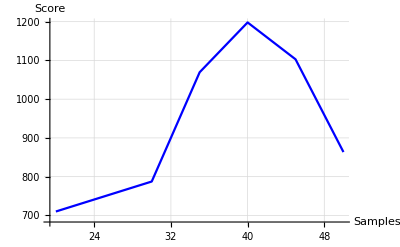

```mathematica
{{hybrid51725Vm = {{20, 0.29}, {30, 0.31}, {35, 0.32}, {40, 0.19}, {45, 0.17}, {50, 0.17}};}, {□}}

(*Tabu 5 1725 Inertia Plot *)

tabu51715InerPlot = ListLinePlot[tabu51725Iner,
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic,
PlotStyle->{Blue}]
```

```mathematica
tabu51725SilPlot = ListLinePlot[tabu51725Sil,
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic, PlotStyle->{Red}];

tabu51725HomogPlot = ListLinePlot[tabu51725Homog,
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic, PlotStyle->{Yellow}];

tabu51725CompPlot = ListLinePlot[tabu51725Comp,
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic, PlotStyle->{Black}];

tabu51725VmPlot = ListLinePlot[tabu51725Vm,
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic, PlotStyle->{Orange}];
```

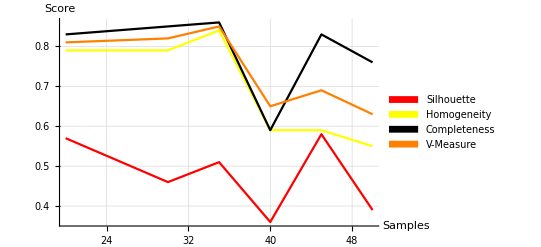

```mathematica
(* Tabu 5 cluster 1725 seed *)
Legended[
Show[tabu51725SilPlot,tabu51725HomogPlot, tabu51725CompPlot,tabu51725VmPlot,
(* PlotLabel-> "Base Formulation: V-Measure", *)
AxesLabel-> {"Samples", "Score"},
PlotRange->All,
GridLines->Automatic],
SwatchLegend[{Red, Yellow, Black, Orange}, {"Silhouette", "Homogeneity", "Completeness", "V-Measure"}]
]
```

```mathematica
(* Sim Annealing 5 1725 *)
```

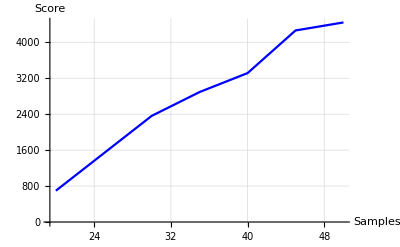

```mathematica
hybrid51715InerPlot = ListLinePlot[sim51725Iner,
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic,
PlotStyle->{Blue}]
```

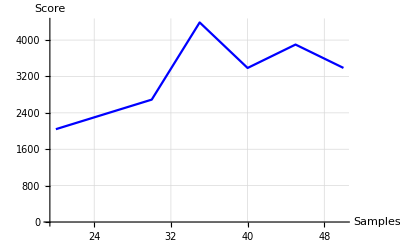

```mathematica
(* Hybrid 5 1725 *)
hybrid51715InerPlot = ListLinePlot[hybrid51725Iner,
AxesLabel->{"Samples", "Score"},
GridLines->Automatic,
PlotRange->Automatic,
PlotStyle->{Blue}]
```

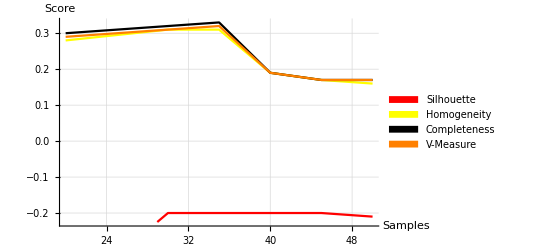

```mathematica
hybrid51725SilPlot=ListLinePlot[hybrid51725Sil,AxesLabel->{"Samples","Score"},GridLines->Automatic,PlotRange->Automatic,PlotStyle->{Red}];

hybrid51725HomogPlot=ListLinePlot[hybrid51725Homog,AxesLabel->{"Samples","Score"},GridLines->Automatic,PlotRange->Automatic,PlotStyle->{Yellow}];

hybrid51725CompPlot=ListLinePlot[hybrid51725Comp,AxesLabel->{"Samples","Score"},GridLines->Automatic,PlotRange->Automatic,PlotStyle->{Black}];

hybrid51725VmPlot=ListLinePlot[hybrid51725Vm,AxesLabel->{"Samples","Score"},GridLines->Automatic,PlotRange->Automatic,PlotStyle->{Orange}];

Legended[Show[hybrid51725SilPlot,hybrid51725HomogPlot,hybrid51725CompPlot,hybrid51725VmPlot,(*PlotLabel->"Base Formulation: V-Measure",*)AxesLabel->{"Samples","Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Yellow,Black,Orange},{"Silhouette","Homogeneity","Completeness","V-Measure"}]]
```

```mathematica
(* Inertia compare 0 seed, 1725 seed  Kmeans *)


km51725Iter = { {20, 5}, {30, 6}, {35, 6}, {40, 5}, {45, 4}, {50, 4}};
km51725Iner = { {20, 19.59},{30, 0.56}, {35, 40.73}, {40, 43.00}, {45, 52.40}, {50, 52.47} };
km51725Sil = { {20, 32.76}, {30, 0.78}, {35, 0.54}, {40, 0.63}, {45, 0.59}, {50, 0.61}};
km51725Homog = {  {20,0.85 },{30, 0.85}, {35, 0.83}, {40, 0.88}, {45, 0.88}, {50, 0.85}};
km51725Comp = { {20, 0.85} ,{30, 0.78}, {35, 0.84}, {40, 0.91}, {45, 0.91}, {50, 0.87}};
km51725Vm = { {20, 0.85}, {30, 0.78}, {35, 0.83}, {40, 0.89}, {45, 0.90},{50, 0.86}};

kmTabu51725Iter = {{20, 3}, {30, 3}, {35, 3}, {40,5 }, {45,9 }, {50, 9}};
kmTabu51725Iner = {{20, 35.45}, {30, 38.64}, {35, 80.97}, {40, 60.41}, {45, 112.56}, {50, 71.15}};
kmTabu51725Sil = {{20, 0.39}, {30, 0.49}, {35, 0.65}, {40, 0.46}, {45, 0.66} ,{50, 0.49}};
kmTabu51725Homog= {{20, 0.73}, {30, 0.75}, {35, 0.59}, {40, 0.76}, {45, 0.59}, {50, 0.74}};
kmTabu51725Comp = {{20, 0.83}, {30, 0.84}, {35, 0.83}, {40, 0.83}, {45, 0.81}, {50, 0.81}};
kmTabu51725Vm = {{20, 0.78}, {30, 0.79}, {35, 0.69}, {40, 0.79} , {45, 0.68}, {50, 0.78}};

kmSim51725Iter={{20, 3}, {30, 4}, {35, 5}, {40, 5}, {45, 5}, {50, 4}};
kmSim51725Iner={{20, 54.43}, {30, 40.18}, {35, 47.14}, {40, 45.77}, {45, 57.62}, {50, 67.83}};
kmSim51725Sil={{20, 0.66}, {30, 0.47}, {35, 0.50}, {40, 0.60}, {45, 0.55}, {50, 0.48}};
kmSim51725Homog={{20, 0.59}, {30, 0.71}, {35, 0.78}, {40, 0.86}, {45, 0.84}, {50, 0.78}};
kmSim51725Comp={{20, 0.82}, {30, 0.78}, {35, 0.82}, {40, 0.86}, {45, 0.86}, {50, 0.79}};
kmSim51725Vm={{20, 0.68}, {30, 0.75}, {35, 0.80}, {40, 0.86}, {45, 0.85}, {50, 0.79}};

kmHybrid51725Iter={{20, 4}, {30, 4}, {35, 8}, {40, 4}, {45, 12}, {50, 4}};
kmHybrid51725Iner={{20, 54.43}, {30, 37.39}, {35, 40.95}, {40, 95.04}, {45, 65.59}, {50, 72.26}};
kmHybrid51725Sil={{20, 0.66}, {30, 0.49}, {35, 0.55}, {40, 0.55}, {45, 0.52}, {50, 0.49}};
kmHybrid51725Homog={{20, 0.59}, {30, 0.82}, {35, 0.78}, {40, 0.59}, {45, 0.82}, {50, 0.74}};
kmHybrid51725Comp={{20, 0.82}, {30, 0.91}, {35, 0.78}, {40, 0.77}, {45, 0.90}, {50, 0.86}};
kmHybrid51725Vm={{20, 0.68}, {30, 0.86}, {35, 0.78}, {40, 0.67}, {45, 0.86}, {50, 0.79}};


(* Kmeans 5 1725 Iteration Comparisons*)

km51725IterNew = { {20, 5}, {30, 6}, {35, 6}, {40, 5}, {45, 4}};
km51725IterNewPlot = ListLinePlot[km51725IterNew, PlotStyle->{Blue}];
```

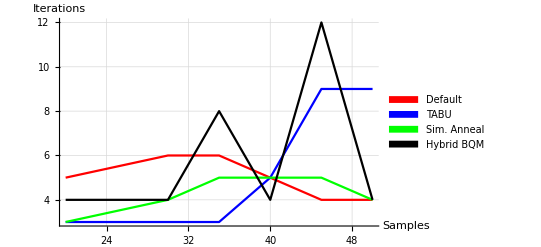

```mathematica
km51725IterPlot= ListLinePlot[km51725Iter, PlotStyle-> {Red}];
kmTabu51725IterPlot= ListLinePlot[kmTabu51725Iter, PlotStyle-> {Blue}];
kmSim51725IterPlot= ListLinePlot[kmSim51725Iter, PlotStyle-> {Green}];
kmHybrid51725IterPlot= ListLinePlot[kmHybrid51725Iter, PlotStyle-> {Black}];

Legended[Show[km51725IterPlot,kmTabu51725IterPlot,kmSim51725IterPlot,kmHybrid51725IterPlot,(*PlotLabel->"Base Formulation: V-Measure",*)AxesLabel->{"Samples","Iterations"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Blue,Green,Black},{"Default","TABU","Sim. Anneal","Hybrid BQM"}]]
```

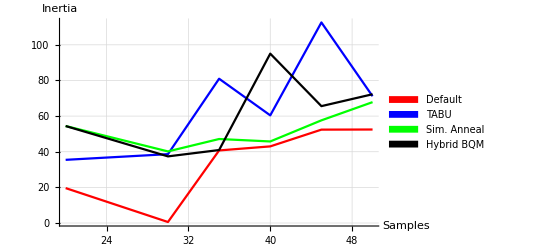

```mathematica
(* 5 1725 Inertia *)
km51725InerPlot=ListLinePlot[km51725Iner,PlotStyle->{Red}];
kmTabu51725InerPlot=ListLinePlot[kmTabu51725Iner,PlotStyle->{Blue}];
kmSim51725InerPlot=ListLinePlot[kmSim51725Iner,PlotStyle->{Green}];
kmHybrid51725InerPlot=ListLinePlot[kmHybrid51725Iner,PlotStyle->{Black}];

Legended[Show[km51725InerPlot,kmTabu51725InerPlot,kmSim51725InerPlot,kmHybrid51725InerPlot,(*PlotLabel->"Base Formulation: V-Measure",*)AxesLabel->{"Samples","Inertia"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Blue,Green,Black},{"Default","TABU","Sim. Anneal","Hybrid BQM"}]]
```

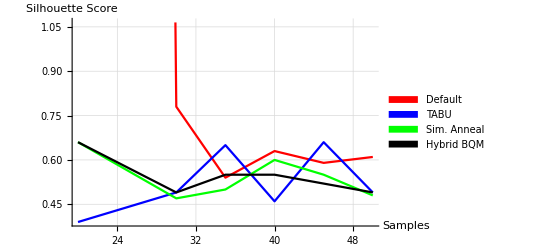

```mathematica
(* Kmeans 5 1725 Silhouette *)

km51725SilPlot=ListLinePlot[km51725Sil,PlotStyle->{Red}];
kmTabu51725SilPlot=ListLinePlot[kmTabu51725Sil,PlotStyle->{Blue}];
kmSim51725SilPlot=ListLinePlot[kmSim51725Sil,PlotStyle->{Green}];
kmHybrid51725SilPlot=ListLinePlot[kmHybrid51725Sil,PlotStyle->{Black}];

Legended[Show[km51725SilPlot,kmTabu51725SilPlot,kmSim51725SilPlot,kmHybrid51725SilPlot,(*PlotLabel->"Base Formulation: V-Measure",*)AxesLabel->{"Samples","Silhouette Score"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Blue,Green,Black},{"Default","TABU","Sim. Anneal","Hybrid BQM"}]]
```

```mathematica
(* kmeans 5 1725 Homogeneity *)
```

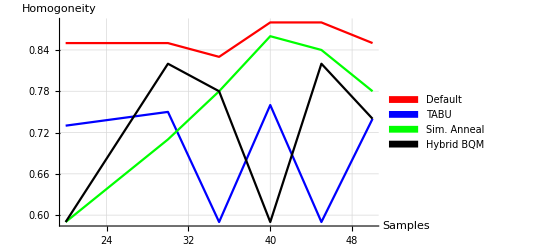

```mathematica
km51725HomogPlot=ListLinePlot[km51725Homog,PlotStyle->{Red}];
kmTabu51725HomogPlot=ListLinePlot[kmTabu51725Homog,PlotStyle->{Blue}];
kmSim51725HomogPlot=ListLinePlot[kmSim51725Homog,PlotStyle->{Green}];
kmHybrid51725HomogPlot=ListLinePlot[kmHybrid51725Homog,PlotStyle->{Black}];

Legended[Show[km51725HomogPlot,kmTabu51725HomogPlot,kmSim51725HomogPlot,kmHybrid51725HomogPlot,(*PlotLabel->"Base Formulation: V-Measure",*)AxesLabel->{"Samples","Homogoneity"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Blue,Green,Black},{"Default","TABU","Sim. Anneal","Hybrid BQM"}]]
```

```mathematica
(* Kmeans 5 1725 Completeness *)
```

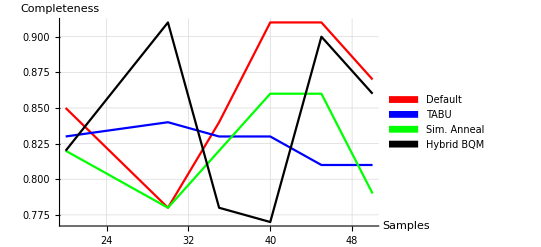

```mathematica
km51725CompPlot=ListLinePlot[km51725Comp,PlotStyle->{Red}];
kmTabu51725CompPlot=ListLinePlot[kmTabu51725Comp,PlotStyle->{Blue}];
kmSim51725CompPlot=ListLinePlot[kmSim51725Comp,PlotStyle->{Green}];
kmHybrid51725CompPlot=ListLinePlot[kmHybrid51725Comp,PlotStyle->{Black}];

Legended[Show[km51725CompPlot,kmTabu51725CompPlot,kmSim51725CompPlot,kmHybrid51725CompPlot,(*PlotLabel->"Base Formulation: V-Measure",*)AxesLabel->{"Samples","Completeness"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Blue,Green,Black},{"Default","TABU","Sim. Anneal","Hybrid BQM"}]]
```

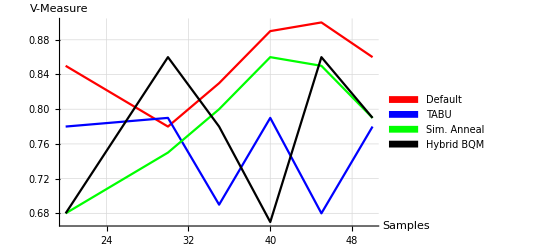

```mathematica
(* Kmeans 5 1725 vmeasure *)

km51725VmPlot=ListLinePlot[km51725Vm,PlotStyle->{Red}];
kmTabu51725VmPlot=ListLinePlot[kmTabu51725Vm,PlotStyle->{Blue}];
kmSim51725VmPlot=ListLinePlot[kmSim51725Vm,PlotStyle->{Green}];
kmHybrid51725VmPlot=ListLinePlot[kmHybrid51725Vm,PlotStyle->{Black}];

Legended[Show[km51725VmPlot,kmTabu51725VmPlot,kmSim51725VmPlot,kmHybrid51725VmPlot,(*PlotLabel->"Base Formulation: V-Measure",*)AxesLabel->{"Samples","V-Measure"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Red,Blue,Green,Black},{"Default","TABU","Sim. Anneal","Hybrid BQM"}]]
```

```mathematica
(* Kmeans comparison both exp Iterations *)
```

```mathematica
{{"[◼]", "PlotGrid"}}[
{
{
kmDefIterPlot,
km51725IterPlot
}
},
FrameLabel->{"x-axis","y-axis"}

]
```

-Graphics-